```mathematica
myFun[z]:=Normal[Series[Exp[-1/x^2]/x,{x,2,200}]]/.x->z
```

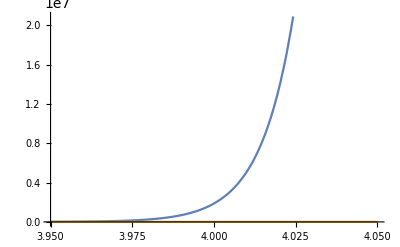

```mathematica
Plot[{myFun[z],Exp[-1/z^2]/z},{z,3.95,4.05}]
```

```mathematica
With[{n=7},CoefficientList[InverseSeries[SeriesData[x,0,Array[a,n],1,n+1,1]],x]]//Simplify
```

{0,1/a[1],-a[2]/a[1]^3,(2 a[2]^2-a[1] a[3])/a[1]^5,-(5 a[2]^3-5 a[1] a[2] a[3]+a[1]^2 a[4])/a[1]^7,(14 a[2]^4-21 a[1] a[2]^2 a[3]+3 a[1]^2 a[3]^2+6 a[1]^2 a[2] a[4]-a[1]^3 a[5])/a[1]^9,1/a[1]^11(-42 a[2]^5+84 a[1] a[2]^3 a[3]-28 a[1]^2 a[2]^2 a[4]+7 a[1]^2 a[2] (-4 a[3]^2+a[1] a[5])+a[1]^3 (7 a[3] a[4]-a[1] a[6])),1/a[1]^13(132 a[2]^6-330 a[1] a[2]^4 a[3]+120 a[1]^2 a[2]^3 a[4]-36 a[1]^2 a[2]^2 (-5 a[3]^2+a[1] a[5])+8 a[1]^3 a[2] (-9 a[3] a[4]+a[1] a[6])+a[1]^3 (-12 a[3]^3+8 a[1] a[3] a[5]+a[1] (4 a[4]^2-a[1] a[7])))}

Compute the series of an inverse function:

```mathematica
x+Sum[x^m/(m! (m-1)!)BellY[Table[{(m+k-2)!,-(k-1)!Subscript[c, k]},{k,2,m}]],{m,2,4}]+O[x]^5
```

x-c_2 x^2+(2 c_2^2-c_3) x^3+(-5 c_2^3+5 c_2 c_3-c_4) x^4+O[x]^5

```mathematica
InverseSeries[x+Subscript[c, 2] x^2+Subscript[c, 3] x^3+Subscript[c, 4] x^4+O[x]^5]//ExpandAll
```

x-c_2 x^2+(2 c_2^2-c_3) x^3+(-5 c_2^3+5 c_2 c_3-c_4) x^4+O[x]^5